# Groups and Algebras

Malcolm Levitt & Christian Bengs 01-July-2023
This documentation applies to SpinDynamica v3.10

more advanced topics use this colour

## Setup

The code in this notebook requires the installation and initialization of SpinDynamica, as described in part 1 of the documentation

```mathematica
Needs["SpinDynamica`"];
SetSpinSystem[3]
SetOperatorBasis[]
```

SpinDynamica version SDv3.9.0b4c loaded by Mathematica 14. running on Mac OS X ARM (64-bit).

SetUserLevel::ini: The user level is being initialized to 2. The user level may be set to an integer between 1 and 3 by using SetUserLevel[level]. Low user levels provide strong syntax trapping at the expense of slow execution for some routines. High user levels relax the syntax trapping in order to provide better execution speeds.

SetUserLevel::ul: The user level has been set to 2.

SetUserLevel::modsymbs: Additional definitions have been given to the following symbols: {Dot,Duration,Exp,Expand,Plus,Power,Simplify,SolidAngle,Times,WignerD}

SpinDynamica::badinfo: In some cases, requesting information by executing "?<symbol>") generates an infinite loop. I have not been able to identify why this happens. In these cases, readable information on a symbol may be generated by executing "<symbol>::usage". Apologies from MHL.

SetSpinSystem::set: the spin system has been set to {{1,1/2},{2,1/2},{3,1/2}}

SetBasis::set: the state basis has been set to ZeemanBasis[{{1,1/2},{2,1/2},{3,1/2}},BasisLabels→Automatic].

SetOperatorBasis::set: the operator basis has been set to ShiftAndZOperatorBasis[{{1,1/2},{2,1/2},{3,1/2}},Sorted→CoherenceOrder].

## Symmetry Groups

### background

Symmetry relations play an important role in the theory of NMR.  Coherence selection rules, phase cycling, recoupling sequences, long-lived spin states, etc. may be rationalised by utilising underlying symmetry relations.

The mathematical machinery to describe the symmetry relations of a given object is given by a symmetry group. A symmetry group consists of all transformations (geometric or abstract) under which the object remains invariant. Consider for example the equilateral triangles shown below:

```mathematica
GraphicsRow[{
Graphics[{
Black,Thickness[0.02],Arrowheads[{0,.05}],Thickness[0.01],
Line[{{0,0},{1,0},{1/2,Sqrt[3]/2},{0,0}}],
Disk[{1/2,Sqrt[3]/4},0.02],
Red,Disk[{0,0},0.05],Blue,Disk[{1,0},0.05],Orange,Disk[{1/2,Sqrt[3]/2},0.05]}],
Graphics[{
Black,Thickness[0.02],Arrowheads[{0,.05}],Thickness[0.01],Arrow@BezierCurve[{1/2,Sqrt[3]/4}+1/8{Cos[#],Sin[#]}&/@(1/3 2π Range[0,1,1/100])],
Line[{{0,0},{1,0},{1/2,Sqrt[3]/2},{0,0}}],
Disk[{1/2,Sqrt[3]/4},0.02],
Orange,Disk[{0,0},0.05],Red,Disk[{1,0},0.05],Blue,Disk[{1/2,Sqrt[3]/2},0.05]}]
,Graphics[{
Black,Thickness[0.02],Arrowheads[{0,.05}],
Thickness[0.01],Arrow@BezierCurve[{1/2,Sqrt[3]/4}+1/8{Cos[#],Sin[#]}&/@(2/3 2π Range[0,1,1/100])],
Line[{{0,0},{1,0},{1/2,Sqrt[3]/2},{0,0}}],
Disk[{1/2,Sqrt[3]/4},0.02],
Blue,Disk[{0,0},0.05],Orange,Disk[{1,0},0.05],Red,Disk[{1/2,Sqrt[3]/2},0.05]}]
}]
```

-Graphics-

The second and the third triangle are related to the first triangle by a 120° and 240° rotation, respectively. Removing the colouring on the other hand would leave the triangle unchanged. The equilateral triangle is thus invariant under 120° and 240° rotations, and its symmetry group is given by:

 G = {R(0°), R(120°), R(240°)}

In the chemistry context molecular point groups represent a convenient way to describe molecular symmetries. The molecular point group consists of all rotations and reflections that do not generate any new molecular conformations when applied to a molecular. 

In general, it is not always immediately obvious how to relate three-dimensional rotations and reflections (the molecular point  group) to the symmetry group of the Hamiltonian (operations that leave the Hamiltonian unchanged). From a spin dynamical point of view it is therefore more convenient to work with spin permutation groups instead of molecular point groups. Consider for example the Hamiltonian of three methyl protons in an isotropic solution:

```mathematica
Hmethyl=ω0 (opI[1,"z"]+opI[2,"z"]+opI[3,"z"])+2π J (opI[1].opI[2]+opI[1].opI[3]+opI[2].opI[3])
```

2 J π (I_(1x)•I_(2x)+I_(1x)•I_(3x)+I_(1y)•I_(2y)+I_(1y)•I_(3y)+I_(1z)•I_(2z)+I_(1z)•I_(3z)+I_(2x)•I_(3x)+I_(2y)•I_(3y)+I_(2z)•I_(3z))+ω0 (I_(1z)+I_(2z)+I_(3z))

Since the Larmor frequency and the J-couplings are identical for all spins, it is not to difficult to see that permuting any of the labels of the spin operators will leave the Hamiltonian unchanged. Consider for example the permutation (12)

```mathematica
Hmethylpermuted=SpinPermutationOperator[{1,2}].Hmethyl.Adjoint[SpinPermutationOperator[{1,2}]]
```

Operator[<<..>>, OperatorType→None ]

```mathematica
Hmethyl-Hmethylpermuted//ExpressOperator
```

0

The spin permutation symmetry of the methyl group Hamiltonian is described by the symmetric group of degree 3 (S_3). This group S_3 is isomorphic to the molecular point group C_(3v), which may be used to describe the local molecular symmetry of a methyl group.

### SpinPermutationGroup

#### spin permutation groups

In SpinDynamica spin permutations groups may be generated utilising the SpinPermutationGroup symbol. For example the spin permutation group of the methyl protons may be generated as follows:

```mathematica
SpinPermutationGroup[{"SymmetricGroup",3}]
```

𝒢[{{1, 1/2}, {2, 1/2}, {3, 1/2}},{SymmetricGroup,3}]

The input consists of the name of the group as a string and its degree.  The output consists of an abstract spin permutation group object, 𝒢, with reference to the group and relevant spins.

Defining spin permutation groups for subsets of the active spin system requires specification of the relevant spins as follows:

```mathematica
SpinPermutationGroup[{1,3},{"SymmetricGroup",2}]
```

𝒢[{{1, 1/2}, {3, 1/2}},{SymmetricGroup,2}]

The output is again abstract, but indicates that spins 1 and 3 are considered to be related by permutation symmetry.

#### Molecular point groups to spin permutation groups

SpinPermutationGroup also supports the use of molecular points groups, which are automatically translated into their spin permutation group analog (this is always possible by virtue of Cayley’s theorem).

For example the molecular point group C_(3v) (Schoenflies notation) is really the same group as S_3 (the two groups are isomorphic). So instead of using the group S_3 SpinPermutationGroup also allows to work with molecular point groups. Unfortunately Mathematica does not support Schoenflies notation, instead the information of the molecular point group C_(3v) is accessed under the {“CrystallographicPointGroup” 18}, which indicates that Mathematica simply enumerates all the 32 fundamental point groups.

```mathematica
SpinPermutationGroup[{"CrystallographicPointGroup",18}]
```

𝒢[{{1, 1/2}, {2, 1/2}, {3, 1/2}},{CrystallographicPointGroup,18}]

A verification that this spin permutation group is indeed equivalent to S_3 may be found in the section about SpinPermutationGroupElements.

A list of all supported molecular point groups (and more) may be found under by executing “FiniteGroupData[]”.

### SpinPermutationGroupElements

An explicit list of the spin permutation group elements may be generated by applying SpinPermutationGroupElements to a spin permutation group object.

```mathematica
groupS3[{1,2,3}]=SpinPermutationGroup[{"SymmetricGroup",3}]
```

𝒢[{{1, 1/2}, {2, 1/2}, {3, 1/2}},{SymmetricGroup,3}]

```mathematica
gelem=SpinPermutationGroupElements[groupS3[{1,2,3}]]
```

{(),(12),(13),(23),(123),(132)}

The output is a list of SpinPermutationOperator objects. The formatting follows the mathematical cycle notation for permutation operations.

Multiplication of two SpinPermutationOperator objects in combination with Operator will simplify the permutation if possible.

```mathematica
gelem⟦3⟧.gelem⟦2⟧
Operator[%]
```

(13)•(12)

(132)

SpinPermutationGroupElements may also be used to verify the equivalence of molecular point groups and spin permutation groups. For example, the equivalence of C_(3v)(within Mathematica known as  {“CrystallographicPointGroup” 18}) and S_3 may be shown by explicitly comparing the group elements:

```mathematica
SpinPermutationGroup[{"CrystallographicPointGroup",18}]
SpinPermutationGroupElements[%]
gelem
```

𝒢[{{1, 1/2}, {2, 1/2}, {3, 1/2}},{CrystallographicPointGroup,18}]

{(),(12),(13),(23),(123),(132)}

{(),(12),(13),(23),(123),(132)}

## Symmetry Adapted Linear Combinations (SALC)

### background

Consider the schematic  water molecule as shown below:

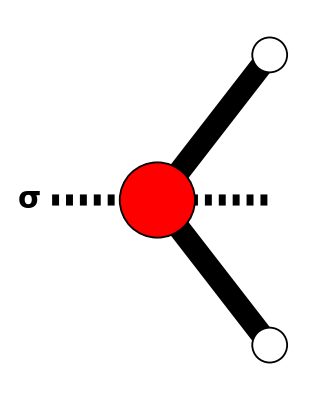

```mathematica
Rotate[Graphics[{
Black,
Thickness[.04],
Line[{{0,0},RotationMatrix[π/180 104.45/2].{1,0}}],Line[{{0,0},RotationMatrix[-π/180 104.45/2].{1,0}}],
Dashed,Thickness[.02],Line[{{0.6,0},{-0.6,0}}],
Rotate[Text[Style["σ",FontSize->30,Bold],{-0.7,0}],π/2],
Disk[RotationMatrix[π/180 104.45/2].{1,0},0.1],Disk[RotationMatrix[-π/180 104.45/2].{1,0},0.1],
White,Disk[RotationMatrix[π/180 104.45/2].{1,0},0.09],Disk[RotationMatrix[-π/180 104.45/2].{1,0},0.09],
Black,Disk[{0,0},0.21],Red,Disk[{0,0},0.2]
}],-π/2]
```

The water molecule is symmetric with respect to a reflection (σ) around the oxygen atom and the trivial operation of doing nothing (e). The symmetry group of the water is thus given by just two elements:

G={e, σ}.

With respect to an appropriate basis we may assign molecular coordinates to the hydrogen atoms:

H_1 = (-r_HH/2,0); H_2 = (+r_HH/2,0) 

The symmetry elements of G may then be represented as matrices:

e = (1 | 0
0 | 1)  and σ = (0 | -1
-1 | 0)

The choice of our basis has been more or less “arbitrary” without any special considerations. The idea of symmetry adapted linear combinations (SALC) is to explicitly take the symmetry of a system into account when constructing a set of basis states. For the hydrogens of the water molecule a more natural choice for the coordinate bases is given by the following SALC’s:

ϕ_1= 1/(√2)(1,1);  ϕ_2= 1/(√2)(1,-1) 

These states explicitly take the symmetry of the hydrogen arrangement into account and may be used to define a basis transformation matrix that takes the system into a symmetry adapted basis:

Φ = (ϕ_1,ϕ_2)

ẽ = ΦeΦ^T = (1 | 0
0 | 1) and σ̃ = ΦσΦ^T = (-1 | 0
0 | 1)

The action (or effect) of the symmetry operations has been considerably simplified, multiplication of any vector by ẽ or σ̃ has been reduced to simply multiplying the elements of the vector by either (+1) or (-1). 

This is the general idea of a symmetry adapted basis, by taking the symmetries of the system explicitly into account the action of a symmetry operation may considerably reduced making the problem more tractable.

### SymmetryAdaptedBasis

The symbol SymmetryAdaptedBasis may be used to construct a set of basis kets that has been symmetrized with respect to a spin permutation group.

SymmetryAdaptedBasis currently provides special support for symmetric and cyclic groups. In this case the syntax takes the form:

SymmetryAdaptedBasis[{{spin1, I1}, {spin2 ,I2}, ...}, {“grouplabel”, groupdegree}]

Here, {spin1,I1}, {spin2,I2},... refers to the spins of interest. The “grouplabel” refers to either “SymmetricGroup” or “CyclicGroup”, note a string is expected.  The groupdegree is an integer referring to the degree of the group.

For arbitrary symmetry groups more information is required and the syntax takes the form:

SymmetryAdaptedBasis[{{spin1, I1}, {spin2 ,I2}, ...}, {{“grouplabel”, groupdegree},Gops}]

The grouplabel is now a free string, and may be chosen by the user, but the groupdegree should match the number of spins. The additional input of Gops refers to a list of the group operators. 

A short-hand syntax is possible if all the active spins are to be considered in the construction of a symmetry-adapted basis:

SymmetryAdaptedBasis[{“grouplabel”, groupdegree}]
SymmetryAdaptedBasis[{{“grouplabel”, groupdegree},Gops}]

#### Symmetric groups

Omitting any arguments for SymmetryAdaptedBasis will always default to a symmetry-adapted basis for the symmetric group taking all active spins into account:

```mathematica
SetSpinSystem[3]
```

SetSpinSystem::set: the spin system has been set to {{1,1/2},{2,1/2},{3,1/2}}

SetBasis::set: the state basis has been set to ZeemanBasis[{{1,1/2},{2,1/2},{3,1/2}},BasisLabels→Automatic].

```mathematica
S3sab=SymmetryAdaptedBasis[]
```

SymmetryAdaptedBasis[{{1,1/2},{2,1/2},{3,1/2}},𝒢[{{1, 1/2}, {2, 1/2}, {3, 1/2}},{SymmetricGroup,3}]]

The basis kets and basis bras may be extracted just as with any other basis set:

```mathematica
BasisKets[S3sab]
BasisBras[S3sab]
```

{|ααα⟩,(|βαα⟩)/(√3)+(|αβα⟩)/(√3)+(|ααβ⟩)/(√3),(|ββα⟩)/(√3)+(|βαβ⟩)/(√3)+(|αββ⟩)/(√3),|βββ⟩,-(|αβα⟩)/(2 √2)+(|ααβ⟩)/(2 √2),-(|ββα⟩)/(√2)+(|αββ⟩)/(√2),-(|ββα⟩)/(√2)+(|βαβ⟩)/(√2),-(3 |βαα⟩)/(2 √2)+(|αβα⟩)/(2 √2)+(|ααβ⟩)/(√2)}

{<ααα|,(<βαα|)/(√3)+(<αβα|)/(√3)+(<ααβ|)/(√3),(<ββα|)/(√3)+(<βαβ|)/(√3)+(<αββ|)/(√3),<βββ|,-(<αβα|)/(2 √2)+(<ααβ|)/(2 √2),-(<ββα|)/(√2)+(<αββ|)/(√2),-(<ββα|)/(√2)+(<βαβ|)/(√2),-(3 <βαα|)/(2 √2)+(<αβα|)/(2 √2)+(<ααβ|)/(√2)}

The irreducible character of the symmetry adapted basis may be verified explicitly by confirming the block diagonal structure of the group element matrix representations:

```mathematica
S3elements=SpinPermutationGroupElements[SpinPermutationGroup[{"SymmetricGroup",3}]]
```

{(),(12),(13),(23),(123),(132)}

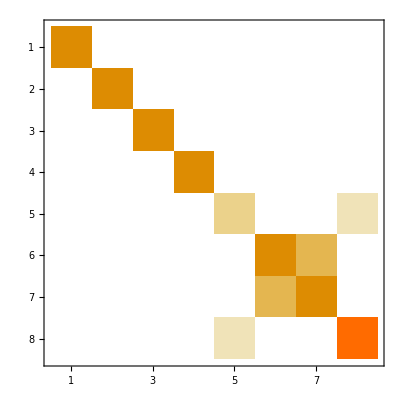
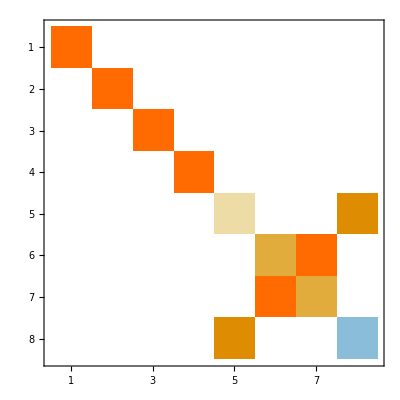
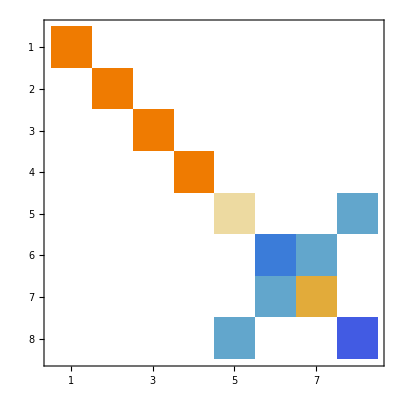
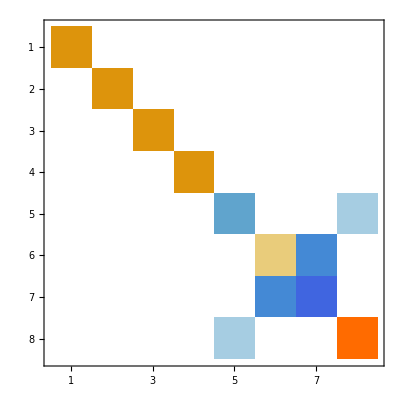
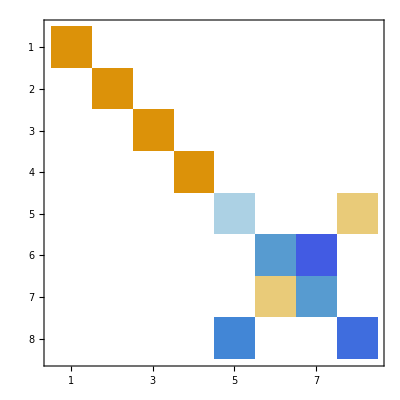
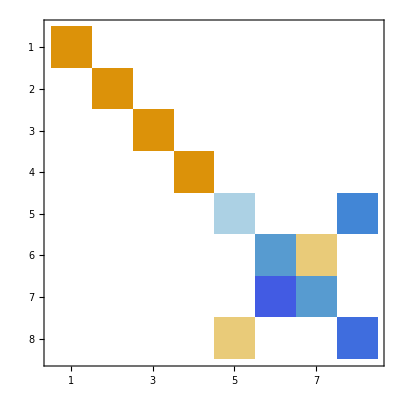

```mathematica
MatrixPlot@Simplify@MatrixRepresentation[#,S3sab]&/@S3elements
```

##### embedded basis

A symmetry adapted basis may also be constructed for a subset of the active spin system, but requires the use of the general syntax for symmetric groups. For example if spins 1 and 2 are related through permutation symmetry, a symmetry-adapted basis may be constructed as follows:

```mathematica
SymmetryAdaptedBasis[{{1,1/2},{2,1/2}},{"SymmetricGroup",2}]
BasisKets[%]
```

SymmetryAdaptedBasis[{{1,1/2},{2,1/2}},𝒢[{{1, 1/2}, {2, 1/2}},{SymmetricGroup,2}]]

{-(|βα⟩)/(√2)+(|αβ⟩)/(√2),|αα⟩,(|βα⟩)/(√2)+(|αβ⟩)/(√2),|ββ⟩}

#### Cyclic groups

Cyclic groups may be handled in similar fashion to symmetric groups:

```mathematica
C3sab=SymmetryAdaptedBasis[{"CyclicGroup",3}]
```

SymmetryAdaptedBasis[{{1,1/2},{2,1/2},{3,1/2}},𝒢[{{1, 1/2}, {2, 1/2}, {3, 1/2}},{CyclicGroup,3}]]

The irreducible character of may be verified explicitly by confirming the block diagonal structure of the group element matrix representations:

```mathematica
C3elements=SpinPermutationGroupElements[SpinPermutationGroup[{"CyclicGroup",3}]]
```

{(),(123),(132)}

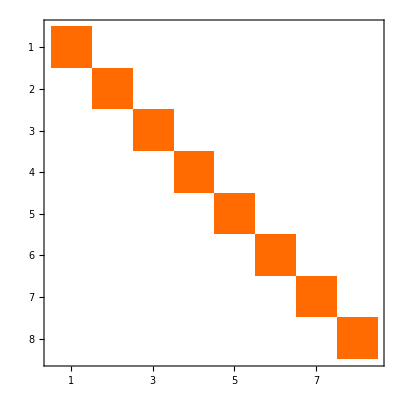
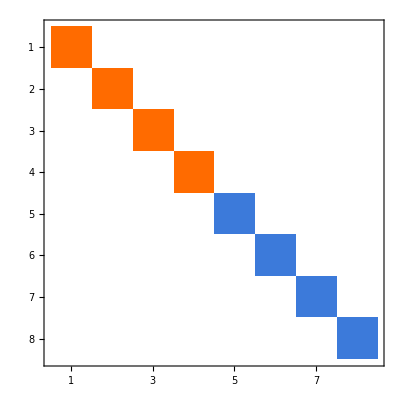
{-Graphics-,-Graphics-,-Graphics-}

```mathematica
MatrixPlot@Simplify@MatrixRepresentation[#,C3sab]&/@C3elements
```

#### Generic groups

Construction of a symmetry-adapted basis with respect to an arbitrary group requires specification of the group elements. 

Consider for example the Dihedral group of degree 3, which represents the symmetry group of an equilateral triangle. The group elements are given by:

```mathematica
D3elements=SpinPermutationGroupElements[SpinPermutationGroup[{"DihedralGroup",3}]]
```

{(),(12),(13),(23),(123),(132)}

A symmetry-adapted basis with respect to the group D_3 may then be defined as follows:

```mathematica
D3sab=SymmetryAdaptedBasis[{{"DihedralGroup",3},D3elements}]
```

SymmetryAdaptedBasis[{{1,1/2},{2,1/2},{3,1/2}},𝒢[{{1, 1/2}, {2, 1/2}, {3, 1/2}},{DihedralGroup,3}]]

The basis kets may be inspected in the usual manner:

```mathematica
BasisKets[D3sab]
```

{1. |ααα⟩,-0.57735 |ββα⟩-0.57735 |βαβ⟩-0.57735 |αββ⟩,1. |βββ⟩,0.57735 |βαα⟩+0.57735 |αβα⟩+0.57735 |ααβ⟩,-0.408248 |βαα⟩-0.408248 |αβα⟩+0.816497 |ααβ⟩,0.707107 |βαα⟩-0.707107 |αβα⟩,-0.816497 |ββα⟩+0.408248 |βαβ⟩+0.408248 |αββ⟩,0.707107 |βαβ⟩-0.707107 |αββ⟩}

Notice that for generic groups the output will in general be in finite precision, not exact arithmetic.

The irreducible character of the basis may be verified explicitly by confirming the block diagonal structure of the group element matrix representations:

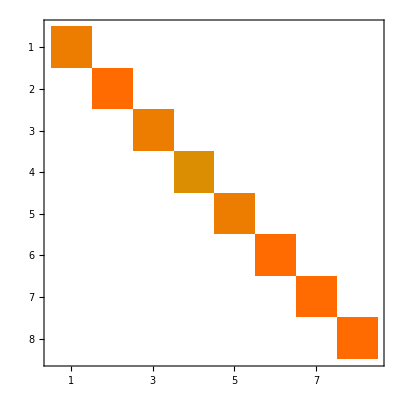
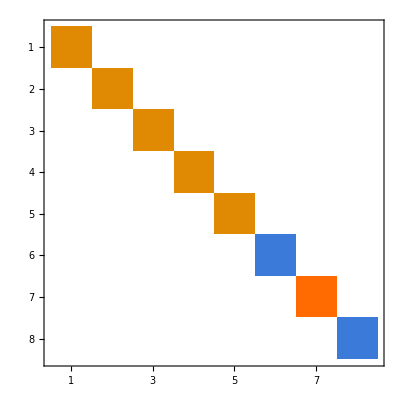
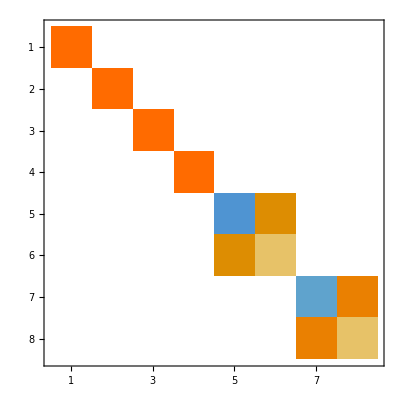
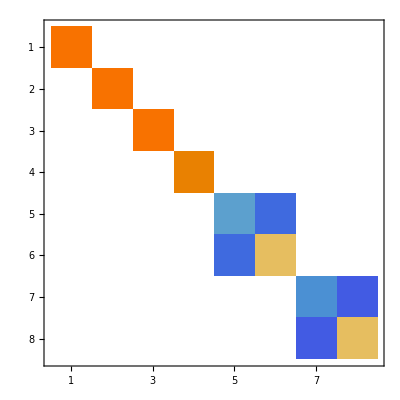
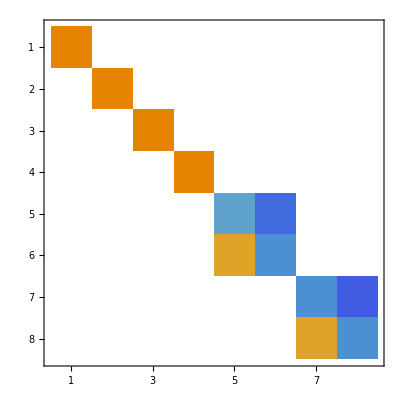
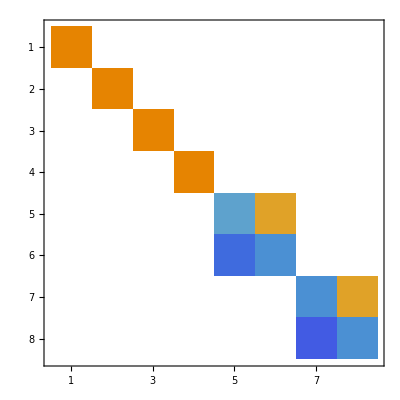

```mathematica
MatrixPlot@Chop@Simplify@MatrixRepresentation[#,D3sab]&/@D3elements
```

## Lie Algebras

### background

Loosely speaking a Lie algebra is a vector space with some “additional” structure. Consider for example our three-dimensional space ℝ^3, the standard basis vectors are 

e_1 = (1, 0, 0) 
e_2 = (0, 1, 0)
e_3 = (0, 0, 1)

Any vector in  ℝ^3 may be expressed as a linear combination of these basis vectors

v = Σ_j x_j e_j

The dot product gives a natural way to extract the coordinates of any vector v

⟨e_j|v⟩ = x_j

Mathematically speaking the dot product takes two vectors as an input and returns a number:

⟨·|·⟩ :  ℝ^3 × ℝ^3 → ℝ

But what about operations that take two vectors in ℝ^3 and generate a new vector in ℝ^3? Perhaps the most familiar operation capable of such a transformation is the three-dimensional cross product.

v × w = (v_2 w_3-v_3 w_2, v_3 w_1-v_1 w_3, v_1 w_2-v_2 w_1)

Mathematically speaking the cross product is of the following type:

· × · :  ℝ^3 × ℝ^3 → ℝ^3

In principle a Lie algebra is not much more than that, it is a vector space with the additional structure of a product rule that takes any two elements of the vector space and returns a new vector space element. This product rule is often called a Lie bracket and denoted by ⟦ ·, ·⟧ . For our three-dimensional space, the cross product (⟦ ·, ·⟧ = · × ·) thus turns ℝ^3 from a vector space into a Lie algebra.

In the quantum context we are typically concerned with evolution of quantum states and the transformation of some initial state vector to some final state vector. As a result, it is perhaps not too surprising that Lie brackets and Lie algebras naturally arise in the description of quantum evolution. 

For example, the evolution of the density operator is governed by the Liouville-von-Neumann equation

d/dt ρ(t) = -i [H, ρ(t)] 

where [H, ρ(t)] refers to the commutator between H and ρ(t)

[H, ρ(t)]  = Hρ(t)-ρ(t)H

Observe that the notation for the commutator ([·,·]) is distinct from the notation for the Lie bracket (⟦ ·, ·⟧). There are subtle differences between the “usual” commutator and the Lie bracket, as discussed further below. The solution to the Liouville-von-Neumann equation may then be expressed as a sum of nested commutators

ρ(t) =U(t)ρ(0)U^†(t) = ρ(0) + (-i t) [H, ρ(0)] + 1/2 (-i t)^2 [H,[H, ρ(0)]] + ...

Since the density operator is required to remain hermitian at all times, it would be nice to know that the r.h.s remains hermitian at all times. For example, does the commutator [X, Y] of two hermitian operators produce a hermitian operator? In other words, does the commutator qualify as a Lie bracket taking two hermitian operators as an input, returning another hermitian operator?

[· , ·] :  Herm × Herm →^(?) Herm

The answer is (perhaps surprisingly) no. Instead, the commutator of two hermitian operators X and Y results in an anti-hermitian operator.

[X, Y]^† = (XY-YX)^† = (YX-XY) = -[X, Y]

However, this problem is easily fixed by defining the Lie bracket as follows

⟦X, Y⟧ = -i [X,Y] ⇒ ⟦X,Y⟧^† = ⟦X,Y⟧

The evolution of the density operator may thus be seen to be given by a sum of Lie brackets

ρ(t) =U(t)ρ(0)U^†(t) = ρ(0) + t ⟦H, ρ(0)⟧ + 1/2 (t)^2 ⟦H,⟦H, ρ(0)⟧⟧ + ...

indicating that the r.h.s remains hermitian. This in turn shows that the space of density operators forms a Lie algebra with the Lie bracket (strictly speaking) not given by the commutator, but instead by a complex commutator

⟦X, Y⟧ = -i [X,Y]

### LieAlgebra

Starting from an initial set of operators {Q_1, Q_2, ...} the LieAlgebra routine generates the corresponding Lie algebra through iterative application of standard Lie bracket (see background). The general syntax is given by:

LieAlgebra[{Q_1, Q_2, ...}, opts]

where {Q_1, Q_2, ...} refers to the initial set of operators and opts to any additional options. 

A standard example is the Lie algebra so(3) of the three-dimensional rotation group. The Lie algebra so(3) may be generated from the following set of operators

```mathematica
SetSpinSystem[1]
```

SetSpinSystem::set: the spin system has been set to {{1,1/2}}

SetBasis::set: the state basis has been set to ZeemanBasis[{{1,1/2}},BasisLabels→Automatic].

```mathematica
so3gen={opI["x"],opI["y"]}
```

{I_(1x),I_(1y)}

```mathematica
LieAlgebra[so3gen]
```

OperatorBasis::inapprop: The current operator basis is inappropriate for the current spin system or the current spin state basis.

SetOperatorBasis::set: the operator basis has been set to ShiftAndZOperatorBasis[{{1,1/2}},Sorted→CoherenceOrder].

{1/2 (I_1^-+I_1^+),1/2 ⅈ (I_1^--I_1^+),I_(1z)}

The result of LieAlgebra is expressed with respect to the active OperatorBasis. Representation with respect to an alternative OperatorBasis may be achieved through the use of the OperatorBasis option

```mathematica
Options[LieAlgebra]
```

{OperatorBasis:>OperatorBasis[],Basis:>Basis[],LieAlgebraField:>R}

```mathematica
LieAlgebra[so3gen,OperatorBasis-> CartesianProductOperatorBasis[]]
```

{I_(1x),I_(1y),I_(1z)}

Notice that this result agrees with the definitions of most standard quantum mechanics textbooks

```mathematica
-I Commutator[opI["x"],opI["y"]]//ExpressOperator
```

I_(1z)

### AbelianSubalgebra

Starting from an initial set of commuting operators {A_1, A_2, ...} the AbelianLieAlgebra routine extends the initial abelian set to a maximal abelian set with respect to some basis operators {B_1, B_2, ...}. The general syntax is given by:

AbelianLieAlgebra[{{A_1, A_2, ...}, {B_1, B_2, ...}}, opts]

The general syntax:

AbelianLieAlgebra[{A_1, A_2, ...}, opts]

extends the set {A_1, A_2, ...} to a maximal abelian subalgebra with respect to all of Liouville space.

```mathematica
SetSpinSystem[2]
```

SetSpinSystem::set: the spin system has been set to {{1,1/2},{2,1/2}}

SetBasis::set: the state basis has been set to ZeemanBasis[{{1,1/2},{2,1/2}},BasisLabels→Automatic].

```mathematica
abeliansubalg=AbelianSubalgebra[{opI[1,"z"].opI[2,"z"]}]
```

SetOperatorBasis::set: the operator basis has been set to ShiftAndZOperatorBasis[{{1,1/2},{2,1/2}},Sorted→CoherenceOrder].

{I_(1z)•I_(2z),I_1^+•I_2^+,I_1^-•I_2^+}

```mathematica
Outer[ExpressOperator@Commutator[#1,#2]&,abeliansubalg,abeliansubalg,1]
```

{{0,0,0},{0,0,0},{0,0,0}}

The result of LieAlgebra is expressed with respect to the active OperatorBasis. Representation with respect to an alternative OperatorBasis may be achieved through the use of the OperatorBasis option

```mathematica
Options[LieAlgebra]
```

{OperatorBasis:>OperatorBasis[],Basis:>Basis[],LieAlgebraField:>R}

```mathematica
AbelianSubalgebra[{opI[1,"z"].opI[2,"z"]},OperatorBasis->CartesianProductOperatorBasis[]]
```

{I_(1z)•I_(2z),2 (I_(1y)•I_(2y)),2 (I_(1x)•I_(2x))}

### Commutant

#### background

Consider a generic Hamiltonian H given by:

H = Σ_j^N x_j X_j

The time-evolution operator for short times may be written as

U(δt) ≃ 1- iδt H

Suppose we are interested in density operator components that are time-invariant.

Q_k(t)=U(t)Q_kU^†(t)=Q_k

In particular this has to hold for small time steps:

Q_k(δt) = U(δt)Q_kU^†(δt) ≃ Q_k -i δt [H,Q_k]

Time-invariance of a particular spin density operator component is thus guaranteed by confirming that

[H,Q_k]= 0 ⇒ [X_j, Q_k] = 0 ∀ j

since the generators are in general linearly-independent.

The routine Commutant goes one step further and answers the reverse question: given a set of generators {X_1, ..., X_N}, what are the spin density operator components Q_k that are time-invariant under an arbitrary Hamiltonian H = Σ_j^N x_j X_j ?

#### examples

Given a set of operators {Q_1, Q_2, ...} the Commutant routine returns the commutant C({Q_1, Q_2, ...}). Elements of C({Q_1, Q_2, ...}) commute with every element in {Q_1, Q_2, ...}. If the operators {Q_1, Q_2, ...} represent a decomposition of the Hamiltonian, the operators C({Q_1, Q_2, ...}) represent the constants of motion, in example the time-invariant spin density operator components. The general syntax is given by:

Commutant[{Q_1, Q_2, ...}, opts]

where {Q_1, Q_2, ...} refers to the initial set of operators and opts to any additional options. 

Consider for example a strongly coupled spin-1/2 system, the corresponding Hamiltonian is generated by the following set of operators

```mathematica
SetSpinSystem[2]
```

SetSpinSystem::set: the spin system has been set to {{1,1/2},{2,1/2}}

SetBasis::set: the state basis has been set to ZeemanBasis[{{1,1/2},{2,1/2}},BasisLabels→Automatic].

```mathematica
Halg={opI[1,"z"]-opI[2,"z"],opI["z"],opI[1].opI[2]}
```

{I_(1z)-I_(2z),I_(1z)+I_(2z),I_(1x)•I_(2x)+I_(1y)•I_(2y)+I_(1z)•I_(2z)}

The time-invariant spin density operator components may simply be calculated via Commutant

```mathematica
commH=Commutant[Halg]
```

OperatorBasis::inapprop: The current operator basis is inappropriate for the current spin system or the current spin state basis.

SetOperatorBasis::set: the operator basis has been set to ShiftAndZOperatorBasis[{{1,1/2},{2,1/2}},Sorted→CoherenceOrder].

{𝟙/2,I_(1z)+I_(2z),2 (I_(1z)•I_(2z))}

This may also be verified explicitly

```mathematica
ExpressOperator@Commutator[#,commH⟦1⟧]&/@Halg
ExpressOperator@Commutator[#,commH⟦2⟧]&/@Halg
ExpressOperator@Commutator[#,commH⟦3⟧]&/@Halg
```

{0,0,0}

{0,0,0}

{0,0,0}

The result above indicates that starting from thermal z-magnetisation it would be impossible to conduct any useful NMR experiments. Of course, this is not too surprising, since we haven’t added in the possibility of applying any pulses. The pulse algebra is given by:

```mathematica
pulsealg={opI["x"],opI["y"]}
```

{I_(1x)+I_(2x),I_(1y)+I_(2y)}

The commutant for the combined algebra of pulses and Hamiltonian dynamics is then given by

```mathematica
Commutant[Join[pulsealg,Halg]]
```

{𝟙/2}

and only consists of the unity element, which trivially commutes with all operators. The pulse algebra in combination with the Hamiltonian algebra is thus enough to manipulate all spin density operator components.

### Bicommutant

Given a set of operators {Q_1, Q_2, ...} the Bicommutant routine calculates the commutant of the commutant of the operators {Q_1, Q_2, ...} , in example C^2({Q_1, Q_2, ...} )=C(C({Q_1, Q_2, ...})). The general syntax is given by:

Bicommutant[{Q_1, Q_2, ...}, opts]

where {Q_1, Q_2, ...} refers to the initial set of operators and opts to any additional options. 

The Bicommutant routine is particularly useful for the calculation of long-lived spin states of a permutation symmetric spin-relaxation process.

Assume for simplicity a fully symmetric three-spin-1/2 system, a rapidly rotating methyl group in solution for example. The symmetry of the three-spin-1/2 system may be described by the symmetric group S_3:

```mathematica
SetSpinSystem[3]
```

SetSpinSystem::set: the spin system has been set to {{1,1/2},{2,1/2},{3,1/2}}

SetBasis::set: the state basis has been set to ZeemanBasis[{{1,1/2},{2,1/2},{3,1/2}},BasisLabels→Automatic].

```mathematica
S3elements=SpinPermutationGroupElements[SpinPermutationGroup[{"SymmetricGroup",3}]]
```

{(),(12),(13),(23),(123),(132)}

An operator is G-symmetric if it commutes with all element of the group G. For the group S_3 this means

Q^* ⇔ [p , Q] = 0 ∀ p ∈ S_3

We use a star to indicate the invariance under a given group.

The set of S_3 symmetric operators is thus given by the commutant of S_3:

```mathematica
Qsym=Commutant[S3elements]
```

OperatorBasis::inapprop: The current operator basis is inappropriate for the current spin system or the current spin state basis.

SetOperatorBasis::set: the operator basis has been set to ShiftAndZOperatorBasis[{{1,1/2},{2,1/2},{3,1/2}},Sorted→CoherenceOrder].

{I_1^+•I_2^+•I_3^+,√2 (I_1^+•I_2^+•I_(3z)+I_1^+•I_(2z)•I_3^++I_(1z)•I_2^+•I_3^+),(I_1^+•I_2^++I_1^+•I_3^++I_2^+•I_3^+)/(√2),1/2 (I_1^++I_2^++I_3^+),2 (I_1^+•I_(2z)•I_(3z)+I_(1z)•I_2^+•I_(3z)+I_(1z)•I_(2z)•I_3^+),I_1^-•I_2^+•I_3^++I_1^+•I_2^-•I_3^++I_1^+•I_2^+•I_3^-,I_1^+•I_(2z)+I_1^+•I_(3z)+I_(1z)•I_2^++I_(1z)•I_3^++I_2^+•I_(3z)+I_(2z)•I_3^+,𝟙/(2 √2),(I_(1z)+I_(2z)+I_(3z))/(√2),2 √2 (I_(1z)•I_(2z)•I_(3z)),√2 (I_1^-•I_2^+•I_(3z)+I_1^-•I_(2z)•I_3^++I_1^+•I_2^-•I_(3z)+I_1^+•I_(2z)•I_3^-+I_(1z)•I_2^-•I_3^++I_(1z)•I_2^+•I_3^-),√2 (I_(1z)•I_(2z)+I_(1z)•I_(3z)+I_(2z)•I_(3z)),(I_1^-•I_2^++I_1^-•I_3^++I_1^+•I_2^-+I_1^+•I_3^-+I_2^-•I_3^++I_2^+•I_3^-)/(√2),1/2 (I_1^-+I_2^-+I_3^-),2 (I_1^-•I_(2z)•I_(3z)+I_(1z)•I_2^-•I_(3z)+I_(1z)•I_(2z)•I_3^-),I_1^-•I_2^-•I_3^++I_1^-•I_2^+•I_3^-+I_1^+•I_2^-•I_3^-,I_1^-•I_(2z)+I_1^-•I_(3z)+I_(1z)•I_2^-+I_(1z)•I_3^-+I_2^-•I_(3z)+I_(2z)•I_3^-,√2 (I_1^-•I_2^-•I_(3z)+I_1^-•I_(2z)•I_3^-+I_(1z)•I_2^-•I_3^-),(I_1^-•I_2^-+I_1^-•I_3^-+I_2^-•I_3^-)/(√2),I_1^-•I_2^-•I_3^-}

The expression below verifies this fact for some random element of the C(S_3):

```mathematica
randQ=RandomChoice[Qsym]
Table[ExpressOperator[g.randQ.Adjoint[g]-randQ],{g,S3elements}]
```

2 (I_1^-•I_(2z)•I_(3z)+I_(1z)•I_2^-•I_(3z)+I_(1z)•I_(2z)•I_3^-)

{0,0,0,0,0,0}

A permutation symmetric spin-relaxation process will in general lead to a permutation symmetric relaxation superoperator. The relaxation superoperator ( Γ̂ ) may then be represented as a linear combination of double-commutation superoperators originating from the set {Q^*}:

Γ̂ = - Σ_k γ_k(OverHat[(Q_k^*]))^†OverHat[Q_k^*]

Since the relaxation superoperator acts through commutation, the condition for an operator Q_LLS to be long-lived is equivalent to demanding that the operator Q_LLS commutes with all operator in the set {Q^*}. In other words an operator is long-lived if and only if it is an element of the commutant of {Q^*}. But since the operators {Q^*} are themselves elements of the commutant of S_3 we may deduce:

Q_LLS ⇔ Q_LLS ∈ C({Q^*}) ⇔ Q_LLS ∈ C(C({S_3})) = C^2({S_3}) 

We may verify this fact explicitly by first calculating the commutant of  {Q^*}

```mathematica
commQsym=Commutant[Qsym]
```

{𝟙/(2 √2),√2 (-(I_1^-•I_2^+•I_(3z))+I_1^-•I_(2z)•I_3^++I_1^+•I_2^-•I_(3z)-I_1^+•I_(2z)•I_3^--I_(1z)•I_2^-•I_3^++I_(1z)•I_2^+•I_3^-),(I_2^-•I_3^++I_2^+•I_3^-+2 (I_(2z)•I_(3z)))/(√2),(I_1^-•I_3^++I_1^+•I_3^-+2 (I_(1z)•I_(3z)))/(√2),(I_1^-•I_2^++I_1^+•I_2^-+2 (I_(1z)•I_(2z)))/(√2)}

and defining an arbitrary S_3 symmetric relaxation superoperator:

```mathematica
Γsym=-Superoperator@Sum[γ[k]DoubleCommutationSuperoperator[Adjoint[Qsym⟦k⟧],Qsym⟦k⟧],{k,1,Length[Qsym]}];
```

The set {Q_LLS} is then indeed in the nullspace of Γ̂

```mathematica
Simplify@ExpressOperator[Γsym[#]]&/@commQsym
```

{0,0,0,0,0}

For convenience this two-step process of calculating the bicommutant of a set of operators  {Q_1, Q_2, ...} is streamlined into the single routine Bicommutant:

```mathematica
QLLS=Bicommutant[S3elements]
```

{𝟙/(2 √2),√2 (-(I_1^-•I_2^+•I_(3z))+I_1^-•I_(2z)•I_3^++I_1^+•I_2^-•I_(3z)-I_1^+•I_(2z)•I_3^--I_(1z)•I_2^-•I_3^++I_(1z)•I_2^+•I_3^-),(I_2^-•I_3^++I_2^+•I_3^-+2 (I_(2z)•I_(3z)))/(√2),(I_1^-•I_3^++I_1^+•I_3^-+2 (I_(1z)•I_(3z)))/(√2),(I_1^-•I_2^++I_1^+•I_2^-+2 (I_(1z)•I_(2z)))/(√2)}

```mathematica
Simplify@ExpressOperator[Γsym[#]]&/@QLLS
```

{0,0,0,0,0}

### InaccesibleOperatorQ

Consider the following question:

What set of operators {F_1, F_2, ...} is inaccessible from a given initial operator Q_i under Hamiltonian evolution described by the set of operators {H_1, H_2, ...}?

The answer to this question may be determined through the use of InaccesibleQ routine. The general syntax follows:

InaccessibleOperatorQ[Q_i → {F_1, F_2, ...}, {H_1, H_2, ...}, opts]

```mathematica
SetSpinSystem[1]

InaccessibleOperatorQ[opI["z"]->{opI["y"]},{opI["z"]}]
```

SetSpinSystem::set: the spin system has been set to {{1,1/2}}

SetBasis::set: the state basis has been set to ZeemanBasis[{{1,1/2}},BasisLabels→Automatic].

OperatorBasis::inapprop: The current operator basis is inappropriate for the current spin system or the current spin state basis.

SetOperatorBasis::set: the operator basis has been set to ShiftAndZOperatorBasis[{{1,1/2}},Sorted→CoherenceOrder].

{True}

```mathematica
InaccessibleOperatorQ[opI["z"]->{opI["y"]},{opI["x"]}]
```

{False}

The results above indicate that y-magnetisation is not accessible from z-magnetisation under a z magnetic field, but becomes accessible through the application of a magnetic field along the x-axis.

Consider the following example for a two-spin-1/2 system:

```mathematica
SetSpinSystem[2]

InaccessibleOperatorQ[opI["z"]->{opI[1,"y"]},{opI["x"]}]
InaccessibleOperatorQ[opI["z"]->{opI[1,"y"]-opI[2,"y"]},{opI["x"]}]
```

SetSpinSystem::set: the spin system has been set to {{1,1/2},{2,1/2}}

SetBasis::set: the state basis has been set to ZeemanBasis[{{1,1/2},{2,1/2}},BasisLabels→Automatic].

OperatorBasis::inapprop: The current operator basis is inappropriate for the current spin system or the current spin state basis.

SetOperatorBasis::set: the operator basis has been set to ShiftAndZOperatorBasis[{{1,1/2},{2,1/2}},Sorted→CoherenceOrder].

{False}

{True}

The results above indicate that I_(1y) (viewed on its own) is accessible from I_(1z)+I_(2z) under a Hamiltonian proportional to I_(1x)+I_(2x). The anti-symmetric combination I_(1y)-I_(2y) however is inaccessible from the symmetric operator I_(1z)+I_(2z) under symmetric evolution generated by I_(1x)+I_(2x).

```mathematica
InaccessibleOperatorQ[opI[1,"z"]-opI[2,"z"]->{opI[1,"y"]-opI[2,"y"]},{opI["x"]}]
```

{False}

The anti-symmetric combination I_(1y)-I_(2y) however becomes accessible under symmetric evolution if the initial state is also anti-symmetric.

## Lie Groups

### Schur-Weyl duality

#### background

The Schur-Weyl duality is a remarkable result from representation theory that relates the irreducible representations of the general linear group to the irreducible representations of the symmetric group in a unique way. 

For typical NMR applications however Schur-Weyl duality theorem is often much more powerful than needed. In very simple terms a generic NMR experiment consists of two ingredients: 

1) the spin Hamiltonian
2) rotations in three-dimensional space

The spin Hamiltonian might possess some type of permutation symmetry, in example two strongly coupled spin-1/2 particles. As a consequence whatever pulse is applied to the system the two spins react identically. In other words in NMR experiments we do not care about relations between the general linear group and the symmetric group, but instead about relations between the three-dimensional rotation group and the symmetric group!

To illustrate the basic ideas we consider two identical spin-1/2 particles described by the Hamiltonian 

H = ω_0(I_(1z)+I_(2z)) + 2π J I_1·I_2

The energy eigenstates of this Hamiltonian are the singlet state and the triplet states.

|S_0⟩ = 1/(√2)(|αβ⟩-|βα⟩), |T_(+1)⟩ = |αα⟩, |T_0⟩ = 1/(√2)(|αβ⟩+|βα⟩), |T_-1⟩ = |ββ⟩

The triplet states are symmetric (g) w.r.t. permutation of spins 1 and 2, whereas the singlet state is anti-symmetric (u) under the same permutation.

(12)|S_0⟩  = (-1) |S_0⟩
(12)|T_m⟩ = (+1)|T_m⟩  

Similarly, the triplet states have total angular momentum of I=1 and transform among each other under rotations, whereas the singlet state has total angular momentum of I=0 and is rotationally invariant. The spin states thus have the following signatures:

|S_0⟩ ↔ (u, I=0) and |T_m⟩ ↔ (g, I=1)

The signatures highlight the fact that spin states with a given permutation symmetry have a well-defined rotational symmetry. This is part of the essence of the Schur-Weyl duality theorem.

#### examples

The routine DualPairing may be used to calculate irreducible representation pairings of the symmetric group S_N and SO(3) considered as a subgroup of  [SU(2I+1)]^(⊗N). The irreducible representations of S_N are represented by their corresponding Young-Tableau, the irreducible representations of SO(3) are labelled according to their total angular momentum value I.

##### two-spin-1/2 systems

The dual pairings for an identical two-spin-1/2 system may be calculated as follows:

```mathematica
DualPairing[2,1/2]
```

|    | ↔ | 𝒟^1 |   
   | ↔ | 𝒟^0

The irreducible representation 𝒟^1 is uniquely associated with Young-Tableau (2,0), whereas the irreducible representation 𝒟^0 is uniquely associated with Young-Tableau (1,1). We may thus identify the Young-Tableau (2,0) with the symmetric representation g, and the Young-Tableau (1,1) with the anti-symmetric representation u.

##### three-spin systems

Consider the case of three identical spins with total angular momentum I. The symmetry group of such a system is S_3, which is isomorphic to C_(3v). The group C_(3v) is known to possess three irreducible representations: {A_1, A_2,  E}. How do these irreducible representations pair up for three identical spin-1/2 particles? The dual pairings for an identical three-spin-1/2 system are given by:

```mathematica
DualPairing[3,1/2]
```

|   
   |  | ↔ | 𝒟^(1/2) |    |    |    | ↔ | 𝒟^(3/2)

The result above shows that 𝒟^(1/2) is uniquely associated with (2,1,0), which corresponds to E, and 𝒟^(3/2) is uniquely associated with (3,0,0), which correspond to A_1. But what about A_2? The A_2 irreducible representation represents spin-states which are totally anti-symmetry under S_3, however since there are only two elementary spins states α and β for a spin-1/2, it is impossible to generate a function which is totally under symmetric under S_3, hence the irreducible representation A_2 is not supported by three identical spin-1/2 systems. 

This suggests that at least three distinct spin states are required to generate the irreducible representation A_2, indeed this is the case as can be seen by considering the dual pairings of a three-spin-1 system:

```mathematica
DualPairing[3,1]
```

| ↔ | 𝒟^0 |    |    |    | ↔ | 𝒟^1 | ⊕ | 𝒟^3
   |   
   |  | ↔ | 𝒟^1 | ⊕ | 𝒟^2 |

Unfortunately the pairing is no longer unique for technical reasons. Nonetheless, the result above has important implications for the number of long-lived states in a deuterated methyl group for example.

#### references

Our method is based on the work of Hermann Jahn (see https://doi.org/10.1098/rspa.1950.0076) by iteratively building up the dual-pairings.